# SM EWPT with Varying Parameters

## T=0 parametrization

```mathematica
V0[ϕ_]:=-1/2 μhsq ϕ^2+λ/4 ϕ^4;
mW[ϕ_]:=1/4 g^2 ϕ^2;
mt[ϕ_]:=1/2 yt^2 ϕ^2;
mZ[ϕ_]:=1/4(g^2+g1^2)ϕ^2;
mH[ϕ_]:=3λ ϕ^2-λ v^2;
VCW[ϕ_]:=1/(64 π^2)(6 mW[ϕ]^2(Log[mW[ϕ]/100^2]-5/6)+3 mZ[ϕ]^2(Log[mZ[ϕ]/100^2]-5/6)-12 mt[ϕ]^2(Log[mt[ϕ]/100^2]-3/2)+mH[ϕ]^2(Log[mH[ϕ]/100^2]-3/2));
V0T[ϕ_]:=V0[ϕ]+VCW[ϕ];
```

```mathematica
vnum=246.22;
mtpole=120.0;
```

```mathematica
num‵rule[g2_,mh_]:=Block[{num},
num={g->g2,mhpole->mh,yt->√2 mtpole/vnum,g1->0.358,v->vnum}];
eqns[g2_,mh_]:={((D[V0T[ϕ],{ϕ,2}]/.{ϕ->v})==mhpole^2)/.num‵rule[g2,mh]//Simplify,((D[V0T[ϕ],ϕ]/.{ϕ->v})==0)/.num‵rule[g2,mh]//Simplify}
```

```mathematica
FindRoot[eqns[0.65,70],{{λ,0.1},{μhsq,70^2/2}}]
```

{λ→0.0417753,μhsq→2659.74}

```mathematica
data=Flatten[Table[{gscan,mhscan,sol=FindRoot[eqns[gscan,mhscan],{{λ,0.1},{μhsq,mhscan^2/2}}];λ/.sol,μhsq/.sol},{gscan,0.5,1.2,0.05},{mhscan,30,70,5}],1];
data=Select[data,#[[3]]∈PositiveReals &];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"SMparam.csv",data];
```

```mathematica
data
```

(0.5 | 30 | 0.00902281 | 690.648
0.5 | 35 | 0.0117082 | 853.121
0.5 | 40 | 0.0148073 | 1040.56
0.5 | 45 | 0.0183198 | 1252.94
0.5 | 50 | 0.0222455 | 1490.24
0.5 | 55 | 0.0265841 | 1752.42
0.5 | 60 | 0.031335 | 2039.46
0.5 | 65 | 0.0364974 | 2351.31
0.5 | 70 | 0.0420705 | 2687.92
0.55 | 30 | 0.00896804 | 683.416
0.55 | 35 | 0.0116535 | 845.889
0.55 | 40 | 0.0147525 | 1033.33
0.55 | 45 | 0.018265 | 1245.71
0.55 | 50 | 0.0221907 | 1483.01
0.55 | 55 | 0.0265293 | 1745.19
0.55 | 60 | 0.0312802 | 2032.23
0.55 | 65 | 0.0364427 | 2344.09
0.55 | 70 | 0.0420158 | 2680.7
0.6 | 30 | 0.00887403 | 674.129
0.6 | 35 | 0.0115594 | 836.603
0.6 | 40 | 0.0146584 | 1024.04
0.6 | 45 | 0.018171 | 1236.42
0.6 | 50 | 0.0220967 | 1473.72
0.6 | 55 | 0.0264353 | 1735.91
0.6 | 60 | 0.0311862 | 2022.96
0.6 | 65 | 0.0363487 | 2334.81
0.6 | 70 | 0.0419219 | 2671.43
0.65 | 30 | 0.00872731 | 662.416
0.65 | 35 | 0.0114127 | 824.891
0.65 | 40 | 0.0145117 | 1012.33
0.65 | 45 | 0.0180242 | 1224.71
0.65 | 50 | 0.0219499 | 1462.02
0.65 | 55 | 0.0262886 | 1724.21
0.65 | 60 | 0.0310395 | 2011.26
0.65 | 65 | 0.0362021 | 2323.12
0.65 | 70 | 0.0417753 | 2659.74
0.7 | 30 | 0.00851214 | 647.87
0.7 | 35 | 0.0111975 | 810.347
0.7 | 40 | 0.0142964 | 997.789
0.7 | 45 | 0.0178089 | 1210.18
0.7 | 50 | 0.0217347 | 1447.48
0.7 | 55 | 0.0260734 | 1709.68
0.7 | 60 | 0.0308244 | 1996.74
0.7 | 65 | 0.035987 | 2308.6
0.7 | 70 | 0.0415603 | 2645.23
0.75 | 30 | 0.00821048 | 630.055
0.75 | 35 | 0.0108958 | 792.535
0.75 | 40 | 0.0139947 | 979.981
0.75 | 45 | 0.0175071 | 1192.37
0.75 | 50 | 0.0214329 | 1429.69
0.75 | 55 | 0.0257716 | 1691.89
0.75 | 60 | 0.0305227 | 1978.95
0.75 | 65 | 0.0356854 | 2290.83
0.75 | 70 | 0.0412589 | 2627.47
0.8 | 30 | 0.00780187 | 608.502
0.8 | 35 | 0.0104871 | 770.984
0.8 | 40 | 0.0135859 | 958.435
0.8 | 45 | 0.0170984 | 1170.83
0.8 | 50 | 0.0210242 | 1408.15
0.8 | 55 | 0.0253629 | 1670.37
0.8 | 60 | 0.0301141 | 1957.44
0.8 | 65 | 0.0352769 | 2269.33
0.8 | 70 | 0.0408506 | 2605.98
0.85 | 30 | 0.00726339 | 582.707
0.85 | 35 | 0.00994846 | 745.194
0.85 | 40 | 0.0130472 | 932.65
0.85 | 45 | 0.0165596 | 1145.06
0.85 | 50 | 0.0204854 | 1382.39
0.85 | 55 | 0.0248242 | 1644.61
0.85 | 60 | 0.0295755 | 1931.7
0.85 | 65 | 0.0347386 | 2243.6
0.85 | 70 | 0.0403125 | 2580.28
0.9 | 30 | 0.00656956 | 552.135
0.9 | 35 | 0.00925446 | 714.627
0.9 | 40 | 0.0123531 | 902.091
0.9 | 45 | 0.0158654 | 1114.51
0.9 | 50 | 0.0197912 | 1351.85
0.9 | 55 | 0.0241301 | 1614.09
0.9 | 60 | 0.0288815 | 1901.2
0.9 | 65 | 0.0340448 | 2213.12
0.9 | 70 | 0.039619 | 2549.82
0.95 | 30 | 0.00569231 | 516.22
0.95 | 35 | 0.00837697 | 678.718
0.95 | 40 | 0.0114754 | 866.19
0.95 | 45 | 0.0149877 | 1078.62
0.95 | 50 | 0.0189134 | 1315.98
0.95 | 55 | 0.0232524 | 1578.24
0.95 | 60 | 0.028004 | 1865.36
0.95 | 65 | 0.0331675 | 2177.31
0.95 | 70 | 0.0387421 | 2514.04
1. | 30 | 0.00460093 | 474.36
1. | 35 | 0.00728523 | 636.864
1. | 40 | 0.0103834 | 824.347
1. | 45 | 0.0138955 | 1036.79
1. | 50 | 0.0178212 | 1274.17
1. | 55 | 0.0221602 | 1536.45
1. | 60 | 0.026912 | 1823.6
1. | 65 | 0.0320758 | 2135.59
1. | 70 | 0.0376509 | 2472.35
1.05 | 30 | 0.003262 | 425.924
1.05 | 35 | 0.00594578 | 588.435
1.05 | 40 | 0.00904361 | 775.929
1.05 | 45 | 0.0125554 | 988.388
1.05 | 50 | 0.016481 | 1225.79
1.05 | 55 | 0.02082 | 1488.1
1.05 | 60 | 0.025572 | 1775.28
1.05 | 65 | 0.0307362 | 2087.31
1.05 | 70 | 0.0363118 | 2424.12
1.1 | 30 | 0.00163948 | 370.248
1.1 | 35 | 0.00432246 | 532.763
1.1 | 40 | 0.0074197 | 720.268
1.1 | 45 | 0.0109311 | 932.745
1.1 | 50 | 0.0148565 | 1170.17
1.1 | 55 | 0.0191955 | 1432.51
1.1 | 60 | 0.0239476 | 1719.74
1.1 | 65 | 0.0291122 | 2031.81
1.1 | 70 | 0.0346884 | 2368.67
1.15 | 35 | 0.00237639 | 469.151
1.15 | 40 | 0.0054727 | 656.666
1.15 | 45 | 0.00898347 | 869.162
1.15 | 50 | 0.0129085 | 1106.61
1.15 | 55 | 0.0172473 | 1368.99
1.15 | 60 | 0.0219996 | 1656.26
1.15 | 65 | 0.0271645 | 1968.39
1.15 | 70 | 0.0327413 | 2305.31
1.2 | 35 | 0.0000662449 | 396.878
1.2 | 40 | 0.00316092 | 584.392
1.2 | 45 | 0.00667064 | 796.904
1.2 | 50 | 0.010595 | 1034.38
1.2 | 55 | 0.0149335 | 1296.8
1.2 | 60 | 0.0196857 | 1584.12
1.2 | 65 | 0.024851 | 1896.31
1.2 | 70 | 0.0304285 | 2233.31)

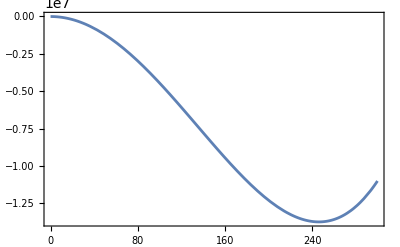

```mathematica
Plot[V0T[ϕ]/.{yt->√2 mtpole/vnum,g1->0.358,v->vnum}/.{λ->0.0145177,μhsq->1012.88,g->0.65}//Re,{ϕ,0,300}]
```

```mathematica
FindMinimum[V0T[ϕ]/.{yt->√2 mtpole/vnum,g1->0.358,v->vnum}/.{λ->0.0145177,μhsq->1012.88,g->0.65}//Re,{ϕ,200}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.37403×10^7,{ϕ→246.249}}

## Phase Transitions

Using Parwani resummation. Data scanned by python with cosmoTransitions.

```mathematica
PTdata=Import[NotebookDirectory[]<>"SMout.csv"];
```

### Tc

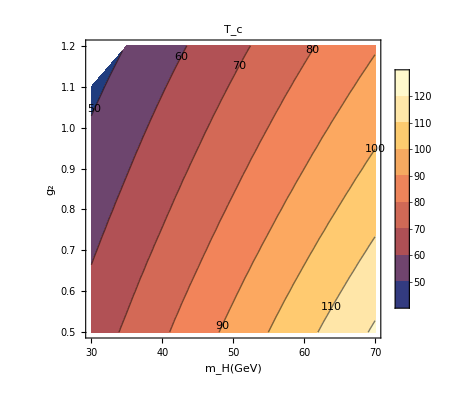

```mathematica
ListContourPlot[PTdata[[All,{2,1,5}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["T_c",FontSize->20]]
```

### T_n

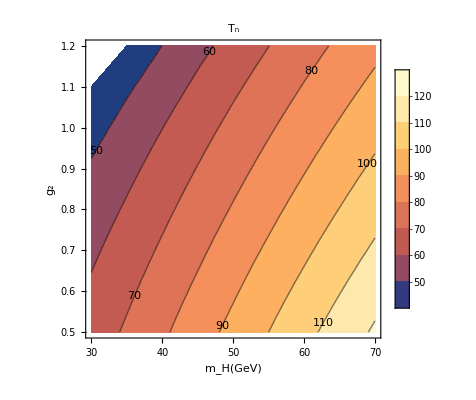

```mathematica
ListContourPlot[PTdata[[All,{2,1,8}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["T_n",FontSize->20]]
```

### T_c-T_n

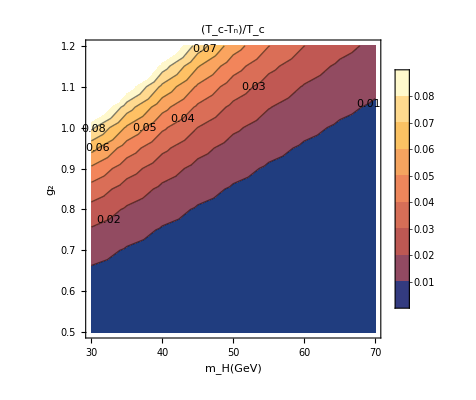

```mathematica
ListContourPlot[{#2,#1,(#5-#8)/#5}&@@@PTdata,FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["(T_c-T_n)/T_c",FontSize->20]]
```

### PT strength at T_c

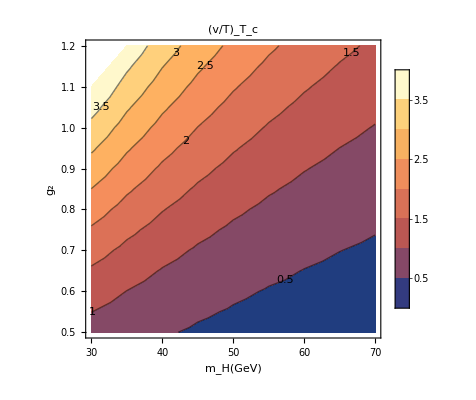

```mathematica
ListContourPlot[PTdata[[All,{2,1,7}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["(v/T)_T_c",FontSize->20]]
```

### PT strength at T_n

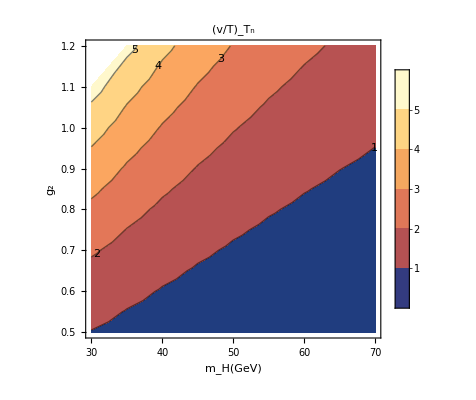

```mathematica
ListContourPlot[PTdata[[All,{2,1,10}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["(v/T)_T_n",FontSize->20]]
```

### Difference of PT strength at T_c and T_n

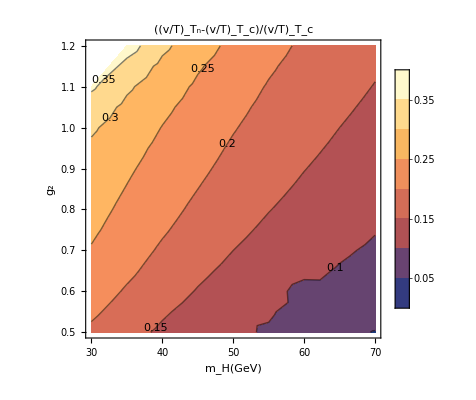

```mathematica
ListContourPlot[{#2,#1,#10/#7-1}&@@@PTdata,FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["((v/T)_T_n-(v/T)_T_c)/(v/T)_T_c",FontSize->20]]
```

### α

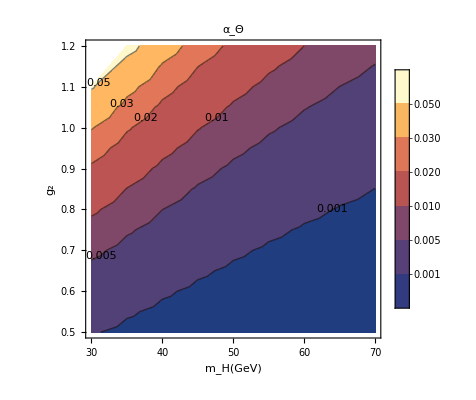

```mathematica
ListContourPlot[PTdata[[All,{2,1,11}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,ContourLabels->All,BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},PlotLabel->Style["α_Θ",FontSize->20],PlotRange->Full,Contours->{0.001,0.005,0.01,0.02,0.03,0.05}]
```

### β/H

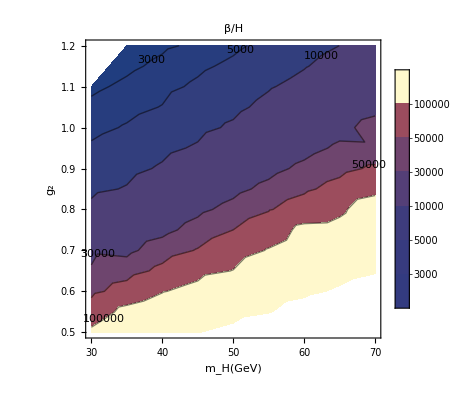

```mathematica
ListContourPlot[PTdata[[All,{2,1,12}]],FrameLabel->{"m_H(GeV)","g_2"},PlotLegends->Automatic,Contours->{3000,5000,10000,30000,50000,100000},BaseStyle->{Directive[InsetBoxOptions->{Background->White},FontFamily->"Times",FontSize->12]},ContourLabels->All,PlotLabel->Style["β/H",FontSize->20]]
```